```mathematica
palette=ImageData[Import["neon.png"]];
palette=Extract[palette,1];
smoothpalette=Interpolation[Table[{(i-1)/(Length[palette]-1),{Extract[Extract[palette,i],1],Extract[Extract[palette,i],2],Extract[Extract[palette,i],3]}},{i,1,Length[palette]}],InterpolationOrder->1];
neon[x_]:=Lighter[RGBColor[smoothpalette[(1-0.999999x)]],0.1];
```

```mathematica
{"log_10(T [d]),log_10(λ [d^-1]),log_10(ℒ),k_1,k_2,median[log_10(ℒ)]_(±1),median[log_10(ℒ)]_(±2)"};
grid=Import[StringJoin[NotebookDirectory[],"output_grid.dat"],"Table"][[8;;All]];
```

```mathematica
Tmin=0.000833333;
Tmax=0.36787944117144233;
λmin=0.01831563888873418;
λmax=7.38905609893065;
Tgrid=Table[Exp[Log[Tmin]+(k-1)*((Log[Tmax]-Log[Tmin])/(100-1))],{k,1,160}];
λgrid=Table[Exp[Log[λmin]+(k-1)*((Log[λmax]-Log[λmin])/(100-1))],{k,1,160}];
Tmin=Min[Tgrid]
Tmax=Max[Tgrid]
λmin=Min[λgrid]
λmax=Max[λgrid]
```

0.000833333

14.7458

0.0183156

280.441

```mathematica
grid2=Table[{Log[Tgrid[[grid[[i,4]]]]],Log[λgrid[[grid[[i,5]]]]],grid[[i,3]],grid[[i,4]],grid[[i,5]],grid[[i,6]],grid[[i,7]]},{i,1,Length[grid]}];
```

```mathematica
N[Log10[0.03]]
```

-1.52288

```mathematica
ListContourPlot[grid2[[All,{1,2,7}]],FrameLabel->{"log_10(duration [days])","log_10(λ [days^-1])"},Contours->{Log10[10^-1.0],Log10[10^-1.25],Log10[10^-1.5],Log10[10^-1.75],Log10[10^-2.0],Log10[10^-2.25],Log10[10^-2.5]},ColorFunction->neon,ColorFunctionScaling->True,ImageSize->Medium,BaseStyle->{FontFamily->"CMU Serif",FontSize->20},InterpolationOrder->2]
```

-Graphics-

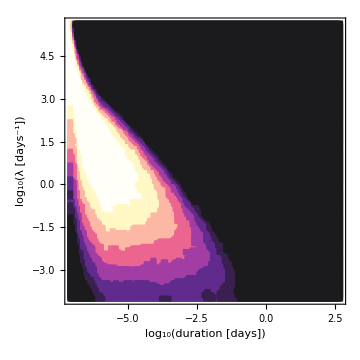

```mathematica
test1=Select[grid2[[All,{1,2,7}]],#[[3]]>Log10[10^-1.0]&][[All,{1,2}]];
test2=Select[grid2[[All,{1,2,7}]],Log10[10^-1.0]≥#[[3]]>Log10[10^-1.25]&][[All,{1,2}]];
test3=Select[grid2[[All,{1,2,7}]],Log10[10^-1.25]≥#[[3]]>Log10[10^-1.5]&][[All,{1,2}]];
test4=Select[grid2[[All,{1,2,7}]],Log10[10^-1.5]≥#[[3]]>Log10[10^-1.75]&][[All,{1,2}]];
test5=Select[grid2[[All,{1,2,7}]],Log10[10^-1.75]≥#[[3]]>Log10[10^-2.00]&][[All,{1,2}]];
test6=Select[grid2[[All,{1,2,7}]],Log10[10^-2.0]≥#[[3]]>Log10[10^-2.25]&][[All,{1,2}]];
test7=Select[grid2[[All,{1,2,7}]],Log10[10^-2.25]≥#[[3]]>Log10[10^-2.5]&][[All,{1,2}]];
test8=Select[grid2[[All,{1,2,7}]],Log10[10^-2.5]≥#[[3]]&][[All,{1,2}]];
ListPlot[{test1,test2,test3,test4,test5,test6,test7,test8},FrameLabel->{"log_10(duration [days])","log_10(λ [days^-1])"},ImageSize->Medium,BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotStyle->{neon[1],neon[1-1/7],neon[1-2/7],neon[1-3/7],neon[1-4/7],neon[1-5/7],neon[1-6/7],neon[0]},Frame->True,Axes->None,PlotRange->{{Log[Tmin],Log[Tmax]},{Log[λmin],Log[λmax]}},AspectRatio->1,PlotMarkers->{"■",6}]
```

```mathematica
{Min[grid2[[All,1]]],Max[grid2[[All,1]]]}
{Min[grid2[[All,2]]],Max[grid2[[All,2]]]}
```

{-7.09008,2.69096}

{-4.,5.63636}

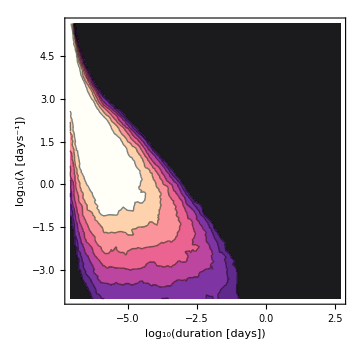

```mathematica
ContourPlot[LOG10LIKE[logT,logλ],{logT,Log[Tmin],Log[Tmax]},{logλ,Log[λmin],Log[λmax]},FrameLabel->{"log_10(duration [days])","log_10(λ [days^-1])"},Contours->{Log10[10^-1.0],Log10[10^-1.25],Log10[10^-1.5],Log10[10^-1.75],Log10[10^-2.0],Log10[10^-2.25],Log10[10^-2.5]},ColorFunction->neon,ColorFunctionScaling->True,ImageSize->Medium,BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotRange->{{Log[Tmin],Log[Tmax]},{Log[λmin],Log[λmax]}}]
```

### MCMC: Walking in log(T) and log(λ) directly

```mathematica
LOG10LIKE=Interpolation[Table[{{grid2[[i,1]],grid2[[i,2]]},grid2[[i,7]]},{i,1,Length[grid2]}]];
```

```mathematica
LOGTMIN=Log[Tmin];LOGTMAX=Log[Tmax];
LOGλMIN=Log[λmin];LOGλMAX=Log[λmax];
```

```mathematica
SeedRandom[42];
ΔLOGT=0.1;ΔLOGλ=0.1;jmax=1.1*10^5;kmax=100;
k=0;Label[kloop];k=k+1;j=1;seed=RandomChoice[Select[grid2,#[[7]]>Log10[0.01]&][[All,{1,2}]]];Subscript[LOGTchain, j]=seed[[1]];Subscript[LOGλchain, j]=seed[[2]];Subscript[LOGLIKE, j]=LOG10LIKE[Subscript[LOGTchain, j],Subscript[LOGλchain, j]]Log[10];tstart=AbsoluteTime[];Label[jloop];LOGTtrial=RandomReal[TruncatedDistribution[{LOGTMIN,LOGTMAX},NormalDistribution[Subscript[LOGTchain, j],ΔLOGT]]];LOGλtrial=RandomReal[TruncatedDistribution[{LOGλMIN,LOGλMAX},NormalDistribution[Subscript[LOGλchain, j],ΔLOGλ]]];LOGLIKEtrial=LOG10LIKE[LOGTtrial,LOGλtrial]Log[10];If[LOGLIKEtrial>Subscript[LOGLIKE, j],accept=1,accept=RandomInteger[BernoulliDistribution[Exp[-Abs[Subscript[LOGLIKE, j]-LOGLIKEtrial]]]]];If[accept==1,j=j+1];If[accept==1,Subscript[LOGTchain, j]=LOGTtrial];If[accept==1,Subscript[LOGλchain, j]=LOGλtrial];If[accept==1,Subscript[LOGLIKE, j]=LOGLIKEtrial];If[j<jmax,Goto[jloop]];Subscript[thischain, k]=Table[{Subscript[LOGTchain, j],Subscript[LOGλchain, j],Subscript[LOGLIKE, j]},{j,1,jmax}][[10001;;jmax]];If[k<kmax,Goto[kloop]];
```

```mathematica
final=Flatten[Table[Subscript[thischain, k],{k,1,kmax}],1];
final=Table[final[[i]],{i,1,Length[final],10}];"thin";
Export[StringJoin[NotebookDirectory[],"mcmc_chain.dat"],final,"Table"]
```

```mathematica
thinner=Table[final[[i]],{i,1,Length[final],10}];
Export[StringJoin[NotebookDirectory[],"mcmc_chain_thinner.dat"],thinner,"Table"]
```

```mathematica
maxloglike=Max[final[[All,3]]]
Exp[maxloglike]
√2 InverseErfc[Exp[maxloglike]]
```

-1.12941

0.323224

0.987853

```mathematica
finalbest=Select[final,#[[3]]==maxloglike&][[1]]
```

{-6.16701,1.30618,-1.12941}

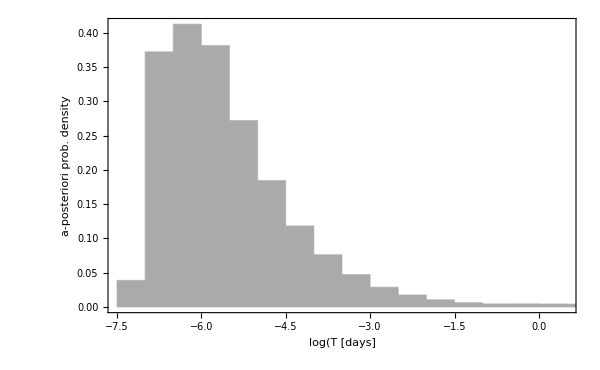

T ∈ [0.00134044 10.4149] days [1σ]

T ∈ [0.000922988 64.1808] days [2σ]

T ∈ [0.000840145 227.117] days [3σ]

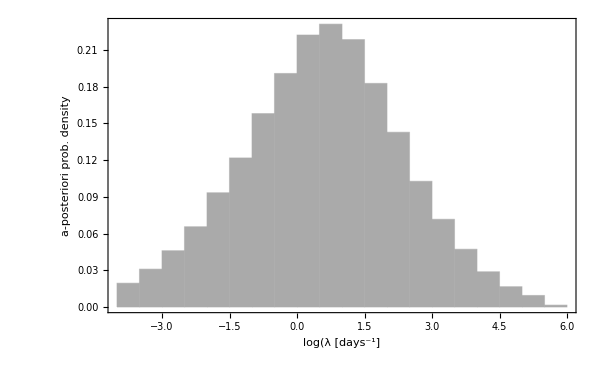

τ ∈ [0.0960163 3.41396] days [1σ]

τ ∈ [0.015581 21.4351] days [2σ]

τ ∈ [0.00440303 49.081] days [3σ]

```mathematica
Histogram[final[[All,1]],Automatic,"PDF",Frame->True,FrameLabel->{"log(T [days]","a-posteriori prob. density"},ImageSize->{600,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},ChartStyle->Lighter[Gray]]
Print["T ∈ [",Exp[Quantile[final[[All,1]],0.5N[Erfc[1/√2]]]]," ",Exp[Quantile[final[[All,2]],1-0.5N[Erfc[1/√2]]]],"] days [1σ]"]
Print["T ∈ [",Exp[Quantile[final[[All,1]],0.5N[Erfc[2/√2]]]]," ",Exp[Quantile[final[[All,2]],1-0.5N[Erfc[2/√2]]]],"] days [2σ]"]
Print["T ∈ [",Exp[Quantile[final[[All,1]],0.5N[Erfc[3/√2]]]]," ",Exp[Quantile[final[[All,2]],1-0.5N[Erfc[3/√2]]]],"] days [3σ]"]
Histogram[final[[All,2]],Automatic,"PDF",Frame->True,FrameLabel->{"log(λ [days^-1]","a-posteriori prob. density"},ImageSize->{600,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},ChartStyle->Lighter[Gray]]
Print["τ ∈ [",1/Exp[Quantile[final[[All,2]],1-0.5N[Erfc[1/√2]]]]," ",1/Exp[Quantile[final[[All,2]],0.5N[Erfc[1/√2]]]],"] days [1σ]"]
Print["τ ∈ [",1/Exp[Quantile[final[[All,2]],1-0.5N[Erfc[2/√2]]]]," ",1/Exp[Quantile[final[[All,2]],0.5N[Erfc[2/√2]]]],"] days [2σ]"]
Print["τ ∈ [",1/Exp[Quantile[final[[All,2]],1-0.5N[Erfc[3/√2]]]]," ",1/Exp[Quantile[final[[All,2]],0.5N[Erfc[3/√2]]]],"] days [3σ]"]
```

```mathematica
kern=SmoothKernelDistribution[final[[All,{1,2}]],Automatic,"Gaussian"];
```

```mathematica
sigmas=Table[{x,N[1-Exp[-x^2/2]]},{x,0,3,0.25}][[2;;All]]
```

{{0.25,0.0307668},{0.5,0.117503},{0.75,0.24516},{1.,0.393469},{1.25,0.542167},{1.5,0.675348},{1.75,0.783735},{2.,0.864665},{2.25,0.92044},{2.5,0.956063},{2.75,0.977206},{3.,0.988891}}

```mathematica
max=NMaximize[{PDF[kern,{LOGT,LOGλ}],LOGTMIN≤LOGT<LOGTMAX,LOGλMIN≤LOGλ<LOGλMAX},{LOGT,LOGλ},Method->"SimulatedAnnealing"];
peak=max[[1]]
```

0.13803

```mathematica
norm=NIntegrate[PDF[kern,{LOGT,LOGλ}],{LOGT,LOGTMIN,LOGTMAX},{LOGλ,LOGλMIN,LOGλMAX},Method->"MonteCarloRule"]
```

0.982639

```mathematica
slots=Table[{x,NIntegrate[Piecewise[{{PDF[kern,{LOGT,LOGλ}]/norm,(PDF[kern,{LOGT,LOGλ}]/norm)≥x peak}}],{LOGT,LOGTMIN,LOGTMAX},{LOGλ,LOGλMIN,LOGλMAX},Method->"MonteCarlo",MaxRecursion->1000]},{x,0,1,0.01}];
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.986045 and 0.0102878 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.96785 and 0.0103752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.959438 and 0.0103807 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

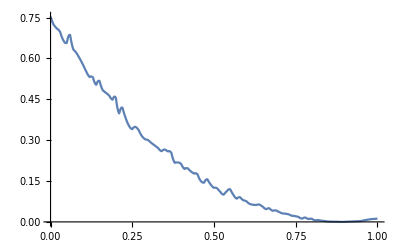

{{0.0307668,0.96749},{0.117503,0.887906},{0.24516,0.760903},{0.393469,0.598161},{0.542167,0.41},{0.675348,0.282123},{0.783735,0.201154},{0.864665,0.106669},{0.92044,0.0668514},{0.956063,0.0259268},{0.977206,0.00420288},{0.988891,0.}}

```mathematica
interp=Interpolation[slots,InterpolationOrder->2];
Plot[(interp[x]-Last[sigmas[[2]]])^2,{x,0,1}]
vala=Table[{Last[sigmas[[i]]],Last[Last[Last[NMinimize[{(interp[x]-Last[sigmas[[i]]])^2,0<x<1},x]]]]},{i,1,Length[sigmas]}]
```

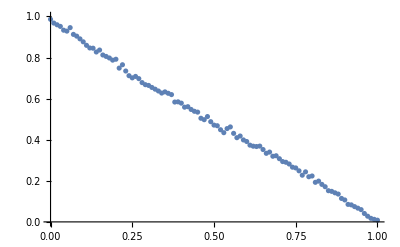

```mathematica
ListPlot[slots,PlotRange->{All,{0,1}}]
```

```mathematica
vala2=vala[[2;;10]];
```

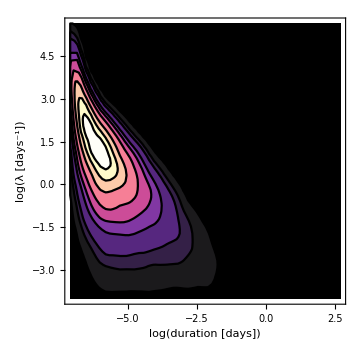

```mathematica
Show[Plot[LOGλMAX+0.1,{LOGT,LOGTMIN,LOGTMAX},PlotRange->{{LOGTMIN,LOGTMAX},{LOGλMIN,LOGλMAX}},FrameLabel->{"log(duration [days])","log(λ [days^-1])"},ImageSize->Medium,BaseStyle->{FontFamily->"CMU Serif",FontSize->20},Frame->True,Axes->None,AspectRatio->1,Filling->LOGλMIN,FillingStyle->Black],Reverse[Table[RegionPlot[PDF[kern,{LOGT,LOGλ}]>peak vala2[[k,2]],{LOGT,LOGTMIN,LOGTMAX},{LOGλ,LOGλMIN,LOGλMAX},PlotRange->{{LOGTMIN,LOGTMAX},{LOGλMIN,LOGλMAX}},BoundaryStyle->Directive[Black],PlotStyle->neon[1-(k-1)/(Length[vala2]-1)]],{k,1,Length[vala2],1}]]]
```

### T histogram

```mathematica
kern1=SmoothKernelDistribution[final[[All,1]],"Silverman","Gaussian"];
max1=NMaximize[{PDF[kern1,x],LOGTMIN<x<LOGTMAX},x]
LOGTMIN2=Last[Last[Last[NMinimize[{(PDF[kern1,x]-10^-9)^2,x<Last[Last[Last[max1]]]},x]]]]
LOGTMAX2=Last[Last[Last[NMinimize[{(PDF[kern1,x]-10^-9)^2,x>Last[Last[Last[max1]]]},x]]]]
```

{0.413992,{x→-6.18582}}

-8.85263

20.3181

```mathematica
split=100;
tabby1=Table[{height,Last[Last[Last[NMinimize[{(PDF[kern1,x]-height)^2,LOGTMIN2<x<Last[Last[Last[max1]]]},x]]]],Last[Last[Last[NMinimize[{(PDF[kern1,x]-height)^2,Last[Last[Last[max1]]]<x<LOGTMAX2},x]]]]},{height,First[max1]/split,First[max1],First[max1]/split}];
xabby1=Table[{tabby1[[i,1]],NIntegrate[PDF[kern1,x],{x,tabby1[[i,2]],tabby1[[i,3]]},Method->"LocalAdaptive"]},{i,1,Length[tabby1]}];
```

```mathematica
sigmasx=Table[{x,Erf[x/√2]},{x,0,3,0.25}][[2;;All]]
```

{{0.25,0.197413},{0.5,0.382925},{0.75,0.546745},{1.,0.682689},{1.25,0.7887},{1.5,0.866386},{1.75,0.919882},{2.,0.9545},{2.25,0.975551},{2.5,0.987581},{2.75,0.99404},{3.,0.9973}}

```mathematica
zigmasx=sigmasx[[2;;10]];
xinterp1=Interpolation[xabby1];
sigmaheights1=Table[{zigmasx[[i,1]],Chop[Last[Last[Last[NMinimize[{(xinterp1[h]-zigmasx[[i,2]])^2,0<h<max1[[1]]},h]]]]]},{i,1,Length[zigmasx]}];
interpleft1=Interpolation[tabby1[[All,{2,1}]]];
interpright1=Interpolation[tabby1[[All,{3,1}]]];
sigmabounds1=Table[{zigmasx[[i,1]],Last[Last[Last[NMinimize[{(interpleft1[x]-sigmaheights1[[i,2]])^2,LOGTMIN<x<LOGTMAX,x<Last[Last[Last[max1]]]},x]]]],Last[Last[Last[NMinimize[{(interpright1[x]-sigmaheights1[[i,2]])^2,LOGTMIN<x<LOGTMAX,Last[Last[Last[max1]]]<x},x]]]]},{i,1,Length[zigmasx]}]
```

InterpolatingFunction::dmval: Input value {2.6253} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.57166} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.6453} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.5,-6.70874,-5.77033},{0.75,-6.89063,-5.49688},{1.,-6.98658,-5.11566},{1.25,-7.05032,-4.67051},{1.5,-7.09008,-4.15964},{1.75,-7.09008,-3.57299},{2.,-7.09008,-2.88208},{2.25,-7.09008,-1.93761},{2.5,-7.09008,-0.89204}}

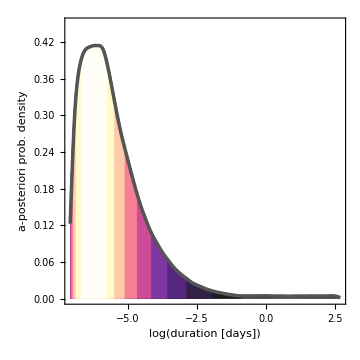

```mathematica
plotrange={{LOGTMIN,LOGTMAX},{0,0.45}};
Show[Plot[0.5,{x,LOGTMIN,LOGTMAX},Frame->True,AspectRatio->1,ImageSize->Medium,FrameLabel->{"log(duration [days])","a-posteriori prob. density"},ImageSize->{600,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},Axes->None,PlotRange->plotrange,Filling->Axis,FillingStyle->Opacity[0]],Plot[PDF[kern1,x],{x,LOGTMIN,LOGTMAX},Filling->0,FillingStyle->neon[0],PlotRange->plotrange],Reverse[Table[Plot[PDF[kern1,x],{x,sigmabounds1[[k]][[2]],sigmabounds1[[k]][[3]]},Filling->0,FillingStyle->neon[1-(k-1)/(Length[zigmasx]-1)],PlotRange->plotrange],{k,1,Length[zigmasx]}]],Plot[PDF[kern1,x],{x,LOGTMIN,LOGTMAX},PlotStyle->Directive[Lighter[Black],Thickness[0.007]]]]
```

```mathematica
sigmabounds1
```

{{0.5,-6.70874,-5.77033},{0.75,-6.89063,-5.49688},{1.,-6.98658,-5.11566},{1.25,-7.05032,-4.67051},{1.5,-7.09008,-4.15964},{1.75,-7.09008,-3.57299},{2.,-7.09008,-2.88208},{2.25,-7.09008,-1.93761},{2.5,-7.09008,-0.89204}}

### λ histogram

```mathematica
kern2=SmoothKernelDistribution[final[[All,2]],"Silverman","Gaussian"];
max2=NMaximize[{PDF[kern2,x],LOGλMIN<x<LOGλMAX},x]
LOGλMIN2=Last[Last[Last[NMinimize[{(PDF[kern2,x]-10^-9)^2,x<Last[Last[Last[max2]]]},x]]]]
LOGλMAX2=Last[Last[Last[NMinimize[{(PDF[kern2,x]-10^-9)^2,x>Last[Last[Last[max2]]]},x]]]]
```

{0.2316,{x→0.697271}}

-4.79427

6.4208

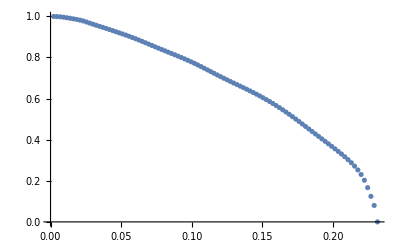

```mathematica
split=100;
tabby2=Table[{height,Last[Last[Last[NMinimize[{(PDF[kern2,x]-height)^2,LOGλMIN2<x<Last[Last[Last[max2]]]},x]]]],Last[Last[Last[NMinimize[{(PDF[kern2,x]-height)^2,Last[Last[Last[max2]]]<x<LOGλMAX2},x]]]]},{height,First[max2]/split,First[max2],First[max2]/split}];
xabby2=Table[{tabby2[[i,1]],NIntegrate[PDF[kern2,x],{x,tabby2[[i,2]],tabby2[[i,3]]},Method->"LocalAdaptive"]},{i,1,Length[tabby2]}];
ListPlot[xabby2]
```

```mathematica
zigmasx=sigmasx[[2;;10]];
xinterp2=Interpolation[xabby2];
sigmaheights2=Table[{zigmasx[[i,1]],Chop[Last[Last[Last[NMinimize[{(xinterp2[h]-zigmasx[[i,2]])^2,0<h<max2[[1]]},h]]]]]},{i,1,Length[zigmasx]}];
interpleft2=Interpolation[tabby2[[All,{2,1}]]];
interpright2=Interpolation[tabby2[[All,{3,1}]]];
sigmabounds2=Table[{zigmasx[[i,1]],Last[Last[Last[NMinimize[{(interpleft2[x]-sigmaheights2[[i,2]])^2,x<Last[Last[Last[max2]]]},x]]]],Last[Last[Last[NMinimize[{(interpright2[x]-sigmaheights2[[i,2]])^2,Last[Last[Last[max2]]]<x},x]]]]},{i,1,Length[zigmasx]}]
```

{{0.5,-0.176683,1.56716},{0.75,-0.654245,1.99973},{1.,-1.16428,2.41919},{1.25,-1.69351,2.84079},{1.5,-2.17621,3.30532},{1.75,-2.67128,3.72192},{2.,-3.15393,4.09079},{2.25,-3.54486,4.43859},{2.5,-3.82089,4.74782}}

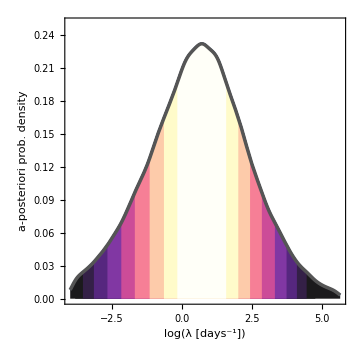

```mathematica
plotrange={{LOGλMIN,LOGλMAX},{0,0.25}};
Show[Plot[0.3,{x,LOGλMIN,LOGλMAX},Frame->True,AspectRatio->1,ImageSize->Medium,FrameLabel->{"log(λ [days^-1])","a-posteriori prob. density"},ImageSize->{600,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},Axes->None,PlotRange->plotrange,Filling->Axis,FillingStyle->Opacity[0]],Plot[PDF[kern2,x],{x,LOGλMIN,LOGλMAX},Filling->0,FillingStyle->neon[0],PlotRange->plotrange],Reverse[Table[Plot[PDF[kern2,x],{x,sigmabounds2[[k]][[2]],sigmabounds2[[k]][[3]]},Filling->0,FillingStyle->neon[1-(k-1)/(Length[zigmasx]-1)],PlotRange->plotrange],{k,1,Length[zigmasx]}]],Plot[PDF[kern2,x],{x,LOGλMIN,LOGλMAX},PlotStyle->Directive[Lighter[Black],Thickness[0.007]]]]
```

```mathematica
sigmabounds2
```

{{0.5,-0.176683,1.56716},{0.75,-0.654245,1.99973},{1.,-1.16428,2.41919},{1.25,-1.69351,2.84079},{1.5,-2.17621,3.30532},{1.75,-2.67128,3.72192},{2.,-3.15393,4.09079},{2.25,-3.54486,4.43859},{2.5,-3.82089,4.74782}}